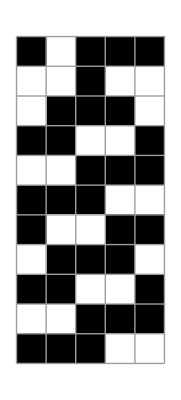

```mathematica
ArrayPlot[ca30,Mesh->True]
```

```mathematica
pattern = {t___,Longest[a__],m___,Longest[a__],___};
```

```mathematica
e = CellularAutomaton[30,{1,0,1,1,1},400];
```

```mathematica
Cases[{e},pattern:> {{t},{m},{a}}];
```

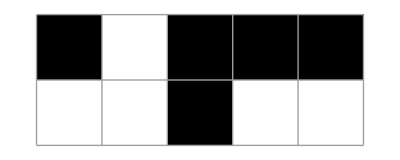
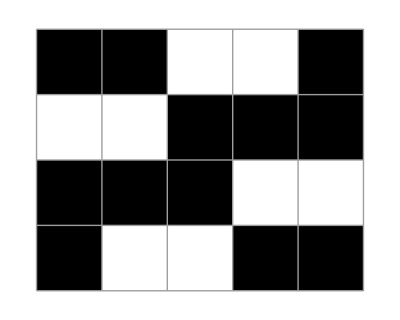
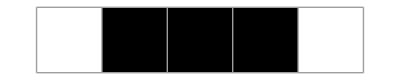

```mathematica
ArrayPlot[#,Mesh->True]&/@
First@Cases[{e},pattern:> {{t},{m},{a}}]
```